```mathematica
H[t_][x_,y_] := Sin[x] + Sin[t] Sin[y]
X[H_][t_]:= Function[{x,y},Evaluate[RotationMatrix[π/2].D[H[t][x,y],{{x,y}}]]]
```

```mathematica
orbit[H_,x0_,y0_] := Module[{sol = NDSolveValue[Thread[{x'[t],y'[t]}==X[H][t][x[t],y[t]]]~Join~{x[0] == x0, y[0]==y0},{x,y},{t,0,2π}]},
Function[t, Mod[Through[sol[t]],2π]]]
flow[p_] := orbit[H, p[[1]],p[[2]]][2π]
```

```mathematica
d[p_, q_] := Sqrt[Sum[Mod[Abs[p[[i]]-q[[i]]],2π]^2, {i,1,2}]]
dev[p_] := d[p,flow[p]]
```

```mathematica
iterate[p_, eps_] := MinimalBy[Table[p+RandomReal[{-eps,eps},2],10],dev][[1]]
```

```mathematica
showOrbits[orbits_] := ParametricPlot[Through[orbits[t]], {t,0,2π}, PlotRange->{{0,2π},{0,2π}}] /. Line[x_]:>{Arrowheads[{0.,0.,0,0.07,0}],Arrow[x]}
```

```mathematica
orbit1 = orbit[H,1,0]
orbit2 = orbit[H,1,1]
```

Function[t$,Mod[Through[sol$4799[t$]],2 π]]

Function[t$,Mod[Through[sol$4831[t$]],2 π]]

1.5708

```mathematica
q = {0.5,3}
```

{0.5,3}

```mathematica
q
dev[q]
```

{0.5,3}

2.0263

```mathematica
iiterate[q_] := Nest[{iterate[#[[1]],1/#[[2]]], #[[2]]+1}&, {q,1},300][[1]]
```

```mathematica
iiterate[{0,0}]
```

{-0.755897,0.0170282}

```mathematica
seeds = Flatten[Table[{x,y},{x,0,2π,0.2},{y,0,2π,0.2}],1];
```

```mathematica
end = Map[iiterate,seeds]
```

$Aborted

{{0.5,3}}

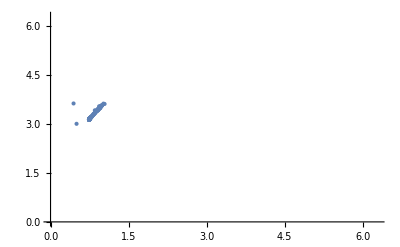

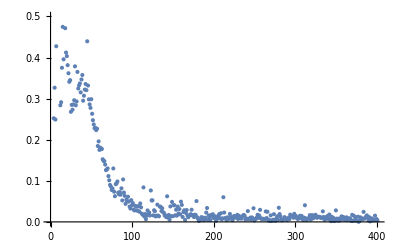

```mathematica
iters = {q}
Do[q = iterate[q,1/i]; AppendTo[iters,q],{i,1,400}]
ListPlot[Mod[iters,2π], PlotRange->{{0,2π},{0,2π}}]
ListPlot[Map[dev,iters],PlotRange->{0,0.5}]
```

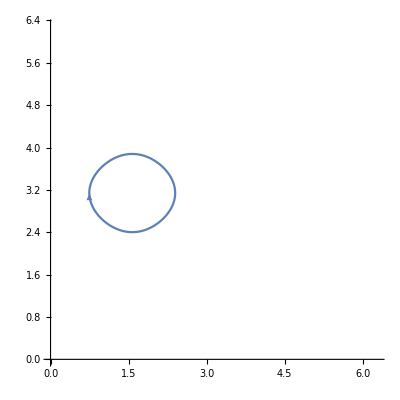

```mathematica
showOrbits[{orbit[H,q[[1]],q[[2]]]}]
```

```mathematica
ArcSin[0.74607875]
```

0.842153

```mathematica
f[x_] := dev[{x,π}]
```

```mathematica
MinimalBy[Table[x,{x,0.74607,0.74609,0.00000001}],f]
```

{0.746079}

7.25116×10^-8

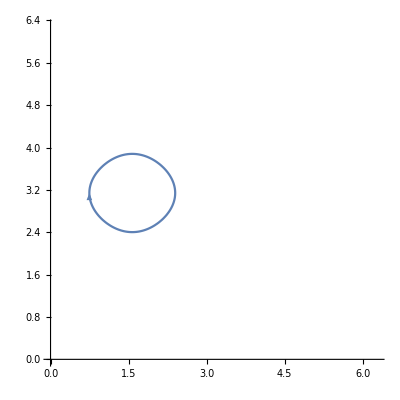

```mathematica
q = {0.74607875,π};
dev[q]
showOrbits[{orbit[H,q[[1]],q[[2]]]}]
```

```mathematica
DSolve[Thread[{x'[t],y'[t]}==X[H][t][x[t],y[t]]]~Join~{x[0] == 0, y[0]==0},{x,y},t]
```

DSolve[{x'[t]==-Cos[y[t]] Sin[t],y'[t]==Cos[x[t]],x[0]==0,y[0]==0},{x,y},t]